```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Get["Methods.m",Path->FileNameJoin[{Directory[],"Packages"}]]

ϵ1=10;
ϵ2=5;
H=12;(*Height of first layer in angstroms*)
a= 3.904;(*unit cell size in angstroms*)
α=.529/a;(*Subscript[a, 0]/a, where Subscript[a, 0] is the Bohr radius*)
t1=.25;(*hopping parameters in eV*)
t2=.025;
MM=10;
NN=4;
β=.95;(*percent of the old distribution to keep when calculating the new distribution*)
numPartitions=20;
numStates=50;

SetParameters[ϵ1,ϵ2,H, a,  t1,t2, MM, NN, β, numPartitions, numStates];

Initialize[]
```

-Graphics3D-

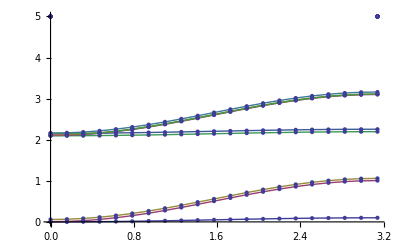

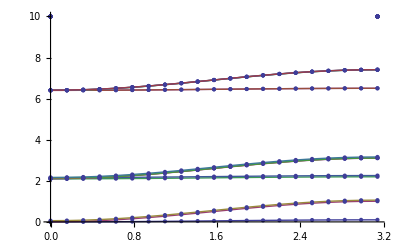

```mathematica
firstGuess=Flatten[Table[
	 N[chargeDist[i ,j ]],
	{i,1,NN},
	{j,1,MM-1}
],1];
firstGuess=totalCharge/(firstGuess//Total)firstGuess;

{listvals,errorList}=SelfConsistentDistribution[firstGuess,.0005];
PlotFullSpaceDistribution[listvals]
bandList=BandStructureList[listvals];
BandStructurePlot[0,5,bandList]
BandStructurePlot[0,10,bandList]
```